```mathematica
rs=1
λ=Sqrt[4]
T=0.1
```

1

2

0.1

```mathematica
kF=(9.0*π/4)^(1/3)/rs
Ef=kF^2
```

1.91916

3.68317

```mathematica
Mom[k_]:=k^2+(-2.0*kF/π)*(1.0+λ/kF*ArcTan[(k-kF)/λ]-λ/kF*ArcTan[(k+kF)/λ]-(λ^2-k^2+kF^2)/4/k/kF*Log[(λ^2+(k-kF)^2)/(λ^2+(k+kF)^2)])
```

```mathematica
f[k_]:=1/(1.0+Exp[(Mom[k]-Mom[kF])/T])
```

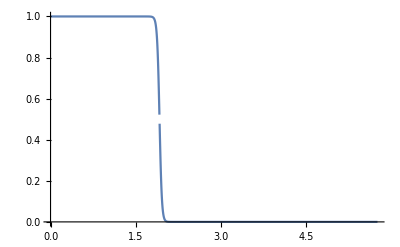

```mathematica
Plot[f[k], {k,0,3*Sqrt[Ef]}]
```

```mathematica
chi=2*1/T*NIntegrate[4*π*k^2*(f[k]^2-f[k]),{k,0, Infinity}]/(2.0*π)^3
```

-0.0942124

```mathematica
NIntegrate[4*π*k^2*f[k], {k,0, Infinity}]/(2.0*π)^3*2
```

0.238943

```mathematica
N[3/(4π*1^3)]
```

0.238732

```mathematica
NIntegrate[4*π*k^2*(f[k]),{k,0, Infinity}]/(2.0*π)^3
```

NIntegrate::inumr: The integrand (4 k^2 π)/(1.+ⅇ^(10. (-3.68317+k^2+1.22177 Plus[«2»]-1.22177 Plus[«4»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

0.00403144 NIntegrate[4 π k^2 f[k],{k,0,∞}]

```mathematica
NIntegrate[4*π*k^2*(f[k]^2),{k,0, Infinity}]/(2.0*π)^3
```

NIntegrate::inumr: The integrand (4 k^2 π)/((1.+ⅇ^(10. («1»)))^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

0.00403144 NIntegrate[4 π k^2 f[k]^2,{k,0,∞}]

```mathematica
chi=2.0*NIntegrate[(f[Sqrt[(kx+3.8683)^2+ky^2+kz^2]]-f[Sqrt[kx^2+ky^2+kz^2]])/((kx+3.8683)^2-kx^2),{kx, -Infinity, Infinity},{ky, -Infinity,Infinity},{kz,-Infinity,Infinity}, PrecisionGoal->4]/(2.0*π)^3
```

NIntegrate::inumr: The integrand (-1/(1.+ⅇ^(10. Plus[«6»]))+1/(1.+ⅇ^(10. (-3.68317+Power[«2»]+«3»+Times[«2»]))))/(-kx^2+(3.8683+kx)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{∞,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.00806288 NIntegrate[(f[√((kx+3.8683)^2+ky^2+kz^2)]-f[√(kx^2+ky^2+kz^2)])/((kx+3.8683)^2-kx^2),{kx,-∞,∞},{ky,-∞,∞},{kz,-∞,∞},PrecisionGoal→4]

```mathematica
chi=2*1/T*NIntegrate[2*π*k*(f[k]^2-f[k]),{k,0, Infinity}]/(2.0*π)^2
```

NIntegrate::inumr: The integrand 2 (1/((1.+ⅇ^(10. (-3.68317+Power[«2»]+Times[«1»]+Times[«2»])))^2)-1/(1.+ⅇ^(10. Plus[«4»]))) k π has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.506606 NIntegrate[2 π k (f[k]^2-f[k]),{k,0,∞}]

```mathematica
chi=2.0*NIntegrate[(f[Sqrt[(kx+0.001)^2+ky^2]]-f[Sqrt[kx^2+ky^2]])/((kx+0.001)^2-kx^2),{kx, -Infinity, Infinity},{ky, -Infinity,Infinity}, PrecisionGoal->4]/(2.0*π)^2
```

NIntegrate::inumr: The integrand (-1/(1.+ⅇ^(10. Plus[«5»]))+1/(1.+ⅇ^(10. (-3.68317+«3»+Times[«2»]))))/(-kx^2+(0.001+kx)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.},{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.0506606 NIntegrate[(f[√((kx+0.001)^2+ky^2)]-f[√(kx^2+ky^2)])/((kx+0.001)^2-kx^2),{kx,-∞,∞},{ky,-∞,∞},PrecisionGoal→4]

```mathematica
Sqrt[Ef]/4/π^2*2
```

0.0972257